## Section | Coherent states

The number states have a uniform phase distribution from 0 to 2π, meaning there is not a defined phase. One may think that the classical limit is when the number of photons of a number state goes to infinity , but that is not the case because the average electric field is zero for any value of quanta. We seek states such that the expectation value of the electric field operator oscillates sinusoidally. Following this idea, we will introduce the coherent states, that are said to be the “most classical” quantum states of light.  We will explore the properties of the coherent states and its connection to the displacement operator.

#### Key Concepts

Classical-like dynamics

Minimum uncertainty states

Poisson statistics

Displacement operator

### Eigenstates of the annihilation operator and minimum uncertainty

If we consider a superposition of number states that differ in ± 1  |ψ⟩ = c_n|n⟩ + c_(n+1)|n+1⟩, it will have non zero expectation for the electric field operator. More generally, a superposition of all number states will also hold that property.

If the annihilation and creation operators, a and a^†, are replaced by complex amplitudes the field can have the structure of a classical field. A reasonable way to try to perform this replacement is to find eigenstates of annihilation operator , in other words solving the eigenvalue equation â|α⟩ = α|α⟩ where α can be in general complex because the operator is not Hermitian.

We can expand the state |α⟩ in the complete Fock basis:

|α⟩ = (∑^)_(n=0)^∞C_n|n⟩

Replacing this expansion in the eigenstate equation and comparing coefficients we get the recurrence relation C_n √n = α C_(n-1)

This recurrence is not hard solve and a compact form can be expressed just in terms of C_0:

```mathematica
FullSimplify[
RSolve[{α C[n-1]- C[n] √n==0,C[0]==Subscript[C, 0]},C[n],n],n ∈PositiveIntegers][[1,1]]
```

C[n]→(α^n C_0)/(√(n!))

So the state |α⟩ can be written as:

|α⟩= C_0(∑^)_(n=0)^∞α^n/(√(n!))|n⟩

Imposing state normalization, we can find C_0 yielding :

```mathematica
FullSimplify[(α^n Subscript[C, 0])/(√(n!))Conjugate[(α^n Subscript[C, 0])/(√(n!))],Subscript[C, 0]∈Reals && n>=0]
```

(C_0^2 Abs[α]^(2 n))/(n!)

```mathematica
Solve[Sum[%,{n,0,∞}]==1,Subscript[C, 0]][[2]]
```

{C_0→ⅇ^(-Abs[α]^2/2)}

So the annihilation operator eigenstate can be expressed as:

|α⟩= ⅇ^(-1/2 |α|^2)(∑^)_(n=0)^∞α^n/(√(n!))|n⟩

This is our first definition of a coherent state in the Fock basis representation

In the Quantum Framework  we can define a normalized coherent state in a truncated Fock space. Within the truncated space, the exponential normalization factor is replaced by its series expansion, truncated at the same order as the Fock space itself

Set up the space size, and the annihilation operator:

```mathematica
SetFockSpaceSize[30];
a := AnnihilationOperator[];
```

For symbolic manipulations can also be useful to define a non-normalized coherent state, which can be done with “Normalized” option:

```mathematica
αket = CoherentState["Normalized"->False];
```

See the formula of the state in Dirac notation:

```mathematica
TraditionalForm@αket
```

0+α1+α^2/(√2)2+α^3/(√6)3+α^4/(2 √6)4+α^5/(2 √30)5+α^6/(12 √5)6+α^7/(12 √35)7+α^8/(24 √70)8+α^9/(72 √70)9+α^10/(720 √7)10+α^11/(720 √77)11+α^12/(1440 √231)12+α^13/(1440 √3003)13+α^14/(10080 √858)14+α^15/(30240 √1430)15+α^16/(120960 √1430)16+α^17/(120960 √24310)17+α^18/(725760 √12155)18+α^19/(725760 √230945)19+α^20/(7257600 √46189)20+α^21/(7257600 √969969)21+α^22/(79833600 √176358)22+α^23/(79833600 √4056234)23+α^24/(958003200 √676039)24+α^25/(4790016000 √676039)25+α^26/(62270208000 √104006)26+α^27/(186810624000 √312018)27+α^28/(2615348736000 √44574)28+α^29/(2615348736000 √1292646)29

Check the normalization of this state is directly related to truncating the exponential as expected:

```mathematica
αket["Norm"] ==√(Normal[Series[ⅇ^-x,{x,0,$FockSize-1}]]/.x->-Abs[α]^2)
```

True

As an example let’s define a coherent state with α=1.3+0.8 ⅈ in a space of dimension 15:

```mathematica
CoherentState[15][1.3+0.8 ⅈ]
```

QuantumState[…]

Right annihilation operator eigenstate property,we compare the amplitudes except the last one because we are using a finite basis:

```mathematica
Most[(a@αket- α αket)["AmplitudesList"]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Define the electric field operator (most general form for a single mode):

Ê= ⅈ √((ℏ ω)/(2 ε_0 V))(â ⅇ^(ⅈ (k · r - ω t))-(â)^†ⅇ^(-ⅈ (k · r - ω t)))

```mathematica
Ex:=ⅈ √((h ω)/(2 V Subscript[ϵ, 0])) (a exp(ⅈ (k.r-t ω))-SuperDagger[a] exp(-ⅈ (k.r-t ω)));
```

Calculate the mean electric field, for some realization of the value of α:

```mathematica
αrandom=2 Exp[ⅈ Exp[RandomReal[{0,2 π}]]];
```

```mathematica
meanEfield =With[{state=CoherentState[][αrandom]},(SuperDagger[state]@Ex@state)["Scalar"]];
```

Classical expression for electric field in terms of complex amplitudes:

ⅈ √((ℏ ω)/(2 ε_0 V))(α ⅇ^(ⅈ(k · r - ω t))-α*ⅇ^(-ⅈ (k ·r - ω t)))

```mathematica
classicalEfield=ⅈ √((h ω)/(2 Subscript[ϵ, 0] V)) (α Exp[ⅈ (k.r-ω t)]-Conjugate[α] Exp[-ⅈ (k.r-ω t)]);
```

Verify the equality:

```mathematica
Chop[meanEfield - (classicalEfield/.α->αrandom)//Simplify]
```

0.+0. ⅈ

Or in polar form α = |α| ⅇ^(ⅈ θ),  we obtain 
⟨α|E_x(r,t)|α⟩=2|α| √((ℏ ω)/(2 ε_0 V))sin(ω t - k ·r-θ):

```mathematica
FullSimplify[classicalEfield/. α->Abs[α] ⅇ^(ⅈ θ) ,Element[{t,ω,k,θ},Reals]]
```

-√2 Abs[α] √((h ω)/(V ϵ_0)) sin(θ+k.r-t ω)

It can be shown that ⟨α|((Ê)_x)^2(r,t)|α⟩= (ℏ ω)/(2 ε_0 V)[1+4|α|^2sin^2(ω t -k·r-θ)] so the fluctuations have this form Δ (Ê)_x=√((ℏ ω)/(2 ε_0 V))

Expectation value of the electric field squared for a coherent state:

```mathematica
meanEfieldSquared = With[{state=CoherentState[][αrandom]},(SuperDagger[state]@(Ex@Ex)@state)["Scalar"]];
```

Electric field fluctuations:

```mathematica
√Chop[FullSimplify[meanEfieldSquared-meanEfield^2]]
```

0.707107 √((h ω)/(V ϵ_0))

This is one of the expressions corresponding to the vacuum fluctuations. It illustrates that a coherent state possesses a classical-like mean field, yet retains the inherent fluctuations of the vacuum state

### Coherent state properties

Another relation explaining the link to vacuum fluctuations is using the quadrature operators  X_i  from chapter 1, a coherent state  minimizes the uncertainty inequality with both quadrature uncertainties being the same

⟨(Δ X_1)^2⟩_α=⟨(Δ X_2)^2⟩_α=1/4

Load the quadrature operators:

```mathematica
{X1,X2} = QuadratureOperators[];
```

Both quadratures variances equal to 1/4, same as the vacuum:

```mathematica
With[{s =CoherentState[][αrandom]},OperatorVariance[s,#]&/@{X1,X2}]//Chop
```

{0.25,0.25}

There is also a relation of α in the phase space context α = ⟨(X̂)_1⟩+ⅈ ⟨(X̂)_2⟩ obtained from seeking states that saturate the uncertainty inequality. It’s possible to solve an eigenvalue equation given that [(X̂)_1,(X̂)_2] = ⅈ/2.

Another measurable aspect of the complex amplitude α is related to the photon number operator, it is easy to verify n^—=⟨α|n|α⟩=|α|^2

Number operator:

```mathematica
numberOp := SuperDagger[a]@a;
```

Mean number of photons of a symbolic coherent state:

```mathematica
meanPho=With[{s=CoherentState[]},(SuperDagger[s]@numberOp@s)["Scalar"]];
```

Plot the mean number of photons (quadratic in |α|):

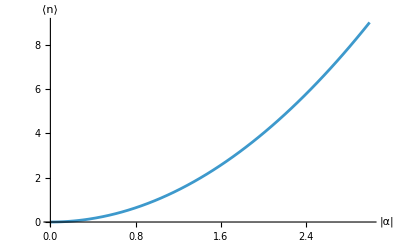

```mathematica
Plot[meanPho,{α,0,3},AxesLabel->{"|α|","⟨n⟩"},LabelStyle->13]
```

Fluctuations of the number operator Δ n =√(|α|^4+|α|^2-(|α|^2)^2)=√(n^—)=|α|

Compute fluctuations for a symbolic coherent state:

```mathematica
fluctuations=√OperatorVariance[CoherentState[],numberOp];
```

Compare to |α|:

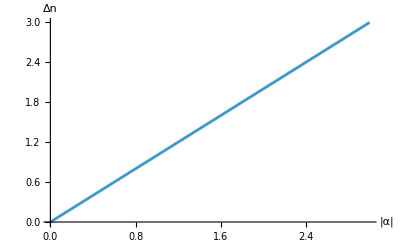

```mathematica
Plot[fluctuations,{α,0,3},AxesLabel->{"|α|","Δn"},LabelStyle->13]
```

This shows that the photon distribution follows a Poisson distribution, this is clearly shown when calculating P_n  the probability of measuring n photons. From the definition of coherent state in Fock basis it is not difficult to obtain:

P_n=ⅇ^(-|α|^2)(|α|^(2n))/(√(n!))=(ⅇ^(- n^—)(n^—)^n)/(√(n!))

The fractional uncertainty (Δ n)/n^—=1/(√(n^—)) decreases with increasing mean photon number. Also the phase distribution for a coherent state |α⟩ (α = |α| ⅇ^(ⅈ θ)) is:

P(ψ)=1/(2 π) |⟨ψ|α⟩|^2

For large |α| the Poisson distribution approximates to a Gaussian so we get the compact expression

P(ψ)≈√(2|α|^2/π) exp(-2|α|^2(ψ-θ)^2)

Plot photon distributions, for |α|^2= 1,2,..10:

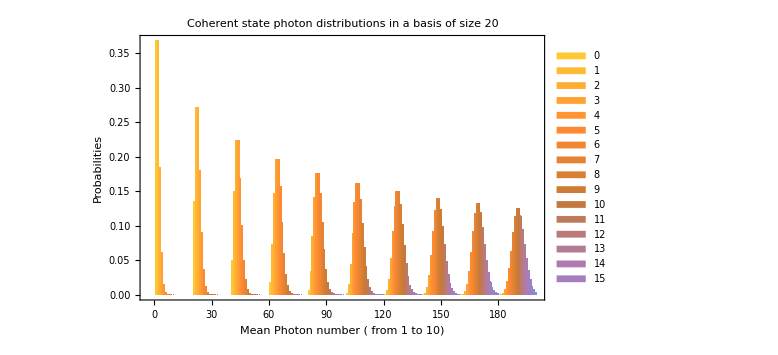

```mathematica
SetFockSpaceSize[20];
BarChart[Table[CoherentState[][√x]["Probabilities"]//Values,{x,1.,10}],]
```

NOTE: Since we are using a truncated basis it is worth noting that to appropriately describe a coherent state with amplitude α, the basis size should be around 
|α |^2+5 |α| (or higher) to completely include the tails of the  Poisson distribution

For  example, for  |α| = √10the best size would be 10+5 √10 ≈ 25:

```mathematica
SetFockSpaceSize[25];
```

We can observe the corresponding photon number distribution:

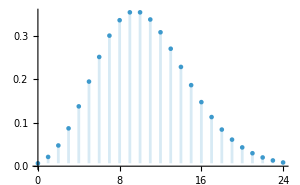

```mathematica
DiscretePlot[Sqrt @ PDF[PoissonDistribution[10],x],{x,0,24},Filling->Bottom,ImageSize->300]
```

“AmplitudesPlot” of the state with the Poisson distribution:

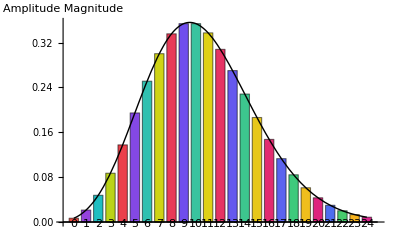

```mathematica
Show[CoherentState[][√10 Exp[ⅈ RandomReal[{0,2π}]]]["AmplitudePlot",LabelStyle->8,ChartLegends->Automatic],,]
```

Plots of phase distributions for different mean photon numbers, becomes more definite when n^— increases:

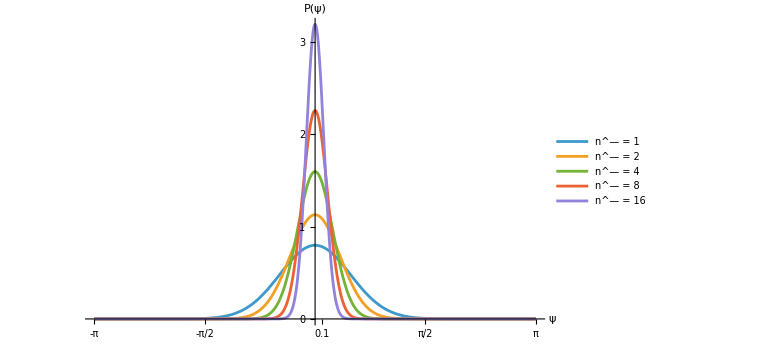

```mathematica
Plot[Evaluate[Table[√((2 Abs[x]^2)/π) Exp[-2 Abs[x]^2 (ψ-Arg[x])^2],{x,{√1,√2,√4,√8,√16}}]],{ψ,-π,π},]
```

So coherent states are quantum states with classical-like  features because:

Mean value of electric field has the form of a classical expression

Electric field fluctuations are those of the vacuum

Fluctuations in the photon number decrease when the mean photon number increases

Their phase becomes more localized when the mean photon number increases

### Displacement operator and displaced vacuum states

There exists an equivalent definition of a coherent state that is based on displacing the vacuum state , it gives more insight why coherent states have must have the uncertainty of the vacuum. The generator is the displacement operator, it is defined as:

D̂(α)= exp(α (â)^†-α*â)

And a coherent state can be build as:

|α⟩=D̂(α)|0⟩

Using the disentangling theorem ⅇ^(Â+B̂)= ⅇ^(Â)ⅇ^(B̂)ⅇ^(-1/2[Â,B̂])  valid when [Â,B̂] ≠ 0  but  [Â,[Â,B̂]] = [B̂,[Â,B̂]] = 0  hold, so the displacement operator takes the following form

D̂(α)= ⅇ^(-1/2 |α|^2)ⅇ^(α (â)^†)ⅇ^(-α* â)

We can check this rearrangement using non-commutative algebra, we just recover the prefactor , because the product of separated terms comes automatically from the Zassenhaus expansion definition ⅇ^(A+B)= ⅇ^A ⅇ^B ∏_(n=2)^∞ ⅇ^(C_n(A,B)) :

Load the Zassenhaus function:

```mathematica
zassen =ResourceFunction["ZassenhausTerms"];
```

Define the algebra:

```mathematica
alg =NonCommutativeAlgebra[<|"ScalarVariables"->α|>];
```

Basic commutator:

```mathematica
rels ={a**SuperDagger[a]-SuperDagger[a]**a-1};
```

Perform the calculation using non-commutative algebra functions, we sum up to the 10th term to show the convergence:

```mathematica
Sum[
NonCommutativePolynomialReduce[
zassen[{α SuperDagger[a],-α*a},n,NonCommutativeMultiply],
rels, {SuperDagger[a],a}, alg ],
{n,2,10}][[-1]]
```

-(α Conjugate[α])/2

In this form we can apply the operator to the vacuum , expanding the first exponential :

ⅇ^(-α* â)|0⟩ =(∑^)_(k=0)^∞((-α* â)^k/(k!))_|0⟩

Now we note that because the annihilation operator and their powers “kill” the vacuum state except when k = 0 , only the vacuum remains. The other exponential can also be expanded

ⅇ^(α (â)^†)|0⟩ =(∑^)_(n=0)^∞(((α (â)^†)^n)/(n!))_|0⟩=(∑^)_(n=0)^∞(α^n/(√(n!)))_|n⟩

because ((â)^†)^n|0⟩ = √(n!)|n⟩,  finally including the normalization constant we see  D(α) |0⟩ is exactly the same as the definition of a coherent state

Verifying symbolically the displacement operator main property , here we are omitting a normalization because quantum state equality works up to a multiplicative global constant:

```mathematica
DisplacementOperator[α][]==CoherentState["Normalized"->False][α]
```

True

Using a truncated basis has additional numeric error propagation because [a, a^†] is not exactly the identity. Using a bigger space size or reducing the magnitude of α can control the desired precision.

Pick a value of α:

```mathematica
αrandom = RandomComplex[{2+2ⅈ,3+3ⅈ}];
```

Try with a “small” truncation size:

```mathematica
SetFockSpaceSize[15];
```

We see appreciable numerical error:

```mathematica
(DisplacementOperator[αrandom][]-CoherentState[][αrandom])["Amplitudes"]//Values
```

{-0.000336592,-0.000713905-0.000952501 ⅈ,0.000835264-0.00285704 ⅈ,0.00569067-0.00213392 ⅈ,0.00905421+0.00578882 ⅈ,0.0012622+0.0169493 ⅈ,-0.0184882+0.0161344 ⅈ,-0.0320781-0.00684038 ⅈ,-0.0172109-0.0372235 ⅈ,0.0229441-0.0425514 ⅈ,0.053467-0.00800768 ⅈ,0.0410244+0.0404985 ⅈ,-0.0079652+0.0583091 ⅈ,-0.0504498+0.028049 ⅈ,-0.0498113-0.0222557 ⅈ}

Use a bigger space size:

```mathematica
SetFockSpaceSize[45];
```

Now the state with this value of α is correctly represented:

```mathematica
(DisplacementOperator[αrandom][]-CoherentState[][αrandom])["Amplitudes"]//Values
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Check the following property (D̂)^†(α) = D̂(-α):

```mathematica
DisplacementOperator[α]["Dagger"] == DisplacementOperator[-α]
```

True

From this it is clear that (D̂)^†(α)D̂(α) = D̂(α) (D̂)^†(α) = 1, so is a unitary operator

Composing two displacement operators also has the form of a displacement operator times an overall phase factor:

D̂(α)D̂(β)= exp(ⅈ Im(α β*))D̂(α + β)

Can be proved using disentangling theorem from the Baker-Campbell-Hausdorff expansion, we see we get the terms of the displacement operator with  z=α + β and the phase factor (z-z*)/2 = ⅈ Im(z).

Load the Baker-Campbell-Hausdorff function:

```mathematica
BCH = ResourceFunction["BakerCampbellHausdorffTerms"];
```

Specify the algebra:

```mathematica
alg =NonCommutativeAlgebra["ScalarVariables"->{α,β}];
```

Compute the result up to seventh order:

```mathematica
Sum[NonCommutativePolynomialReduce[
BCH[{α SuperDagger[a]-α*a,β SuperDagger[a]-β*a},n,NonCommutativeMultiply],
rels,
{SuperDagger[a],a},
alg][[-1]],{n,1,7}]
```

(α+β) a^†+a (-Conjugate[α]-Conjugate[β])-(β Conjugate[α])/2+(α Conjugate[β])/2

Intuitively if we do a displacement of α and then a displacement of β, the net displacement is α + β, so we get a coherent state with amplitude α + β up to a global phase:

D̂(α)D̂(β)|0⟩=D̂(α)|β⟩=exp(ⅈ Im(α β*)) |α + β⟩

Pick values of α and β:

```mathematica
SeedRandom[100];
{αrandom,βrandom}= RandomComplex[{-2-2I,2+2I},2];
```

We consider a bigger size because are composing displacements:

```mathematica
SetFockSpaceSize[50];
```

Composition of displacement operators:

```mathematica
composedDisplacement =DisplacementOperator[αrandom]@DisplacementOperator[βrandom][];
```

Result using the coherent |α + β ⟩:

```mathematica
coherentresult =Exp[ⅈ Im[αrandom βrandom*]]CoherentState[][αrandom + βrandom];
```

“AmplitudeList” returns non zero amplitudes, in this case all are zero so the states are the numerically the same:

```mathematica
Chop[composedDisplacement-coherentresult]["AmplitudeList"]
```

{}

### Wave packets and time evolution

The position operator q̂ is defined, such that q̂ |q⟩ = q |q⟩ describes the position eigenstates, in terms of ladder operators can be written as:

q̂ =√(ℏ/(2 m ω))(â+(â)^†) =√(ℏ/(m ω))OverHat[X_1]

```mathematica
SetFockSpaceSize[20];
```

Define the position operator:

```mathematica
q = √(h/(m ω)) QuadratureOperators[][[1]];
```

The Fock states wave functions are the following (derivations can be found in standard quantum mechanics textbooks regarding a quantum harmonic oscillator):

ψ_n(q)= ((m ω)/(π ℏ))^(1/4)(2^n n!)^(-1/2)H_n(ξ)exp(-ξ^2/2)

where ξ= q √(m ω/ℏ) and H_n are Hermite polynomials:

Then the wave function for a coherent state is:

ψ_α(q)=⟨q|α⟩ = ((m ω)/(π ℏ))^(1/4)ⅇ^(-|α|^2/2)ⅇ^(-ξ^2/2) (∑^)_(n=0)^∞(α/√2)^n/(n!) H_n(ξ)

It can be simplified and it takes the form of a gaussian, and the probability distribution |ψ_α(q)|^2 also takes the form of a gaussian

Perform the simplification symbolically:

```mathematica
waveFuncCoh =((m ω)/(π h))^(1/4)ⅇ^(-Abs[α]^2/2)ⅇ^(-ξ^2/2)ⅇ^(ξ^2)FullSimplify[(ⅇ^(-ξ^2) Sum[(z)^n/n!HermiteH[n,ξ],{n,0,∞}])]/.z->α/√2;
```

Show the result:

```mathematica
TraditionalForm[waveFuncCoh]
```

(ⅇ^(-(α/(√2)-ξ)^2-Abs[α]^2/2+ξ^2/2) ((m ω)/h)^(1/4))/π^(1/4)

Plot when α = 1:

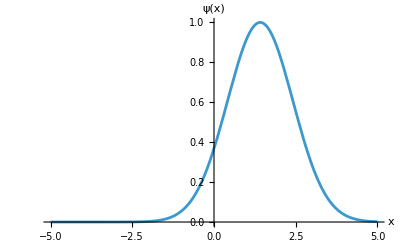

```mathematica
Plot[waveFuncCoh[[1]] /. α->1,{ξ,-5,5},AxesLabel->{"x","ψ(x)"},LabelStyle->12]
```

The diagonal quantum harmonic oscillator Hamiltonian for a single mode field:

```mathematica
H = h ω (SuperDagger[a]@a +1/2 );
```

See the Dirac notation:

```mathematica
H//TraditionalForm
```

(h ω)/2 00+(3 h ω)/2 11+(5 h ω)/2 22+(7 h ω)/2 33+(9 h ω)/2 44+(11 h ω)/2 55+(13 h ω)/2 66+(15 h ω)/2 77+(17 h ω)/2 88+(19 h ω)/2 99+(21 h ω)/2 1010+(23 h ω)/2 1111+(25 h ω)/2 1212+(27 h ω)/2 1313+(29 h ω)/2 1414+(31 h ω)/2 1515+(33 h ω)/2 1616+(35 h ω)/2 1717+(37 h ω)/2 1818+(39 h ω)/2 1919

We create an evolution operator to evolve the states at any time:

```mathematica
QOE=QuantumEvolve[H/h,None,t];
```

A coherent state  remains a coherent state under the evolution , however the complex amplitude phase depends on time  with an extra global phase 
|ψ(t)⟩ = ⅇ^(-ⅈ ω t/2)|α ⅇ^(-ⅈ ω t)⟩:

```mathematica
(QOE @ CoherentState[]) == ⅇ^(-ⅈ ω t/2)CoherentState[][α ⅇ^(-ⅈ ω t)]
```

True

The mean value of the position operator for the evolved state behaves like it is a classical oscillator (sinusoidal oscillations). This emphasizes another reason why coherent states are called “the most classical” quantum states. This also holds for the mean value of the momentum operator.

Pick a value of α:

```mathematica
αc = RandomComplex[√2{-1-ⅈ,1+ⅈ}];
```

Evolve states:

```mathematica
states=Table[{t,QOE[t][CoherentState[][αc]]},{t,0,10,0.25}];
```

Calculate expectations of position operator:

```mathematica
meanPosition=MapAt[((SuperDagger[#]@q@#)["Scalar"]&),#,2]& /@ states ;
```

Plot the results:

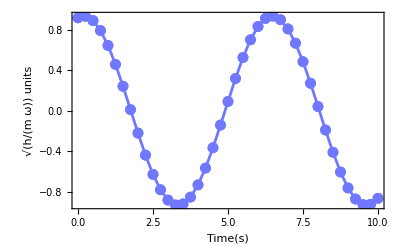

```mathematica
ListLinePlot[Re[meanPosition/.{h->1,m->1,ω->1}],]
```

### Additional properties of coherent states

The  inner  product   of  two  coherent  states | α⟩,  | β ⟩ is:

⟨β |α⟩ =exp(-1/2(β*α-β α*)) exp(-1/2|β-α|^2)

So when α and β are different clearly the states are not orthogonal , but when the quantity |β - α|^2 is large the states are almost orthogonal ( ⟨ β | α⟩ ≈ 0)

Choose values of α and β:

```mathematica
{αc,βc} = RandomComplex[{1.5+1.5I},2];
```

Compute the bracket:

```mathematica
(CoherentState[][αc]["Dagger"]@CoherentState[][βc])["Scalar"]
```

0.537487-0.435223 ⅈ

Use the analytical expression:

```mathematica
Exp[-1/2(βc*αc-βc αc*)]Exp[-1/2 Abs[βc-αc]^2]
```

0.537487-0.435223 ⅈ

The coherent states have a completeness relation  over the complex α plane given by:

∫ |α⟩⟨α|(ⅆ^2 α)/π=1

We include the exact normalization constant so we can try to reproduce the theoretical results, we use a Fock space size of 5 just to take a look at the matrix elements of |α⟩⟨α|:

```mathematica
With[{s=CoherentState[5,"Normalized"->False]},Exp[-Abs[α]^2](s@SuperDagger[s])]
```

ⅇ^(-Abs[α]^2)00+ⅇ^(-Abs[α]^2) Conjugate[α]01+(ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(√2)02+(ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(√6)03+(ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(2 √6)04+α ⅇ^(-Abs[α]^2)10+α ⅇ^(-Abs[α]^2) Conjugate[α]11+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(√2)12+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(√6)13+(α ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(2 √6)14+(α^2 ⅇ^(-Abs[α]^2))/(√2)20+(α^2 ⅇ^(-Abs[α]^2) Conjugate[α])/(√2)21+1/2 α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^2 22+(α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^3)/(2 √3)23+(α^2 ⅇ^(-Abs[α]^2) (Conjugate[α])^4)/(4 √3)24+(α^3 ⅇ^(-Abs[α]^2))/(√6)30+(α^3 ⅇ^(-Abs[α]^2) Conjugate[α])/(√6)31+(α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(2 √3)32+1/6 α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^3 33+1/12 α^3 ⅇ^(-Abs[α]^2) (Conjugate[α])^4 34+(α^4 ⅇ^(-Abs[α]^2))/(2 √6)40+(α^4 ⅇ^(-Abs[α]^2) Conjugate[α])/(2 √6)41+(α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^2)/(4 √3)42+1/12 α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^3 43+1/24 α^4 ⅇ^(-Abs[α]^2) (Conjugate[α])^4 44

The integrals of the matrix elements in Cartesian coordinates, can be demanding computationally:

```mathematica
Integrate[1/24 α^4 ⅇ^(-Abs[α]^2) Conjugate[α]^4/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{59.1393,π}

```mathematica
Integrate[(α^3 ⅇ^(-Abs[α]^2) Conjugate[α]^2)/(√12)/.α->x+y ⅈ,{x,-∞,∞},{y,-∞,∞}]//AbsoluteTiming
```

{18.4519,0}

The m,n  matrix element of the result is

O_(m,n) =1/(√(m! n!))∫ⅇ^(-|α|^2)(α^m(α*))^n ⅆ^2 α

switching to polar coordinates α = r e^(ⅈ θ), ⅆ^2 α = r ⅆr ⅆθ

∫_0^∞ r^(m+n+1)ⅇ^(-r^2)ⅆr ∫_0^(2π) ⅇ^(ⅈ θ(m-n))ⅆθ

We evaluate the integral for general m and n separating in cases when m and n are equal or not, showing the completeness relation:

```mathematica
Table[{assump,
FullSimplify[
Integrate[Sqrt[1/(m! n!)] r^(m+n+1) Exp[-r^2] Exp[I (m-n) θ],{r,0,∞},{θ,0,2 π},Assumptions->assump],Element[{m,n},Integers]&&n>=0&&m>=0]},
{assump,{m==n,m != n}}] //
TableForm[#,TableHeadings->{None,{"Case", "Result"}}]&
```

Case | Result
m==n | π
m≠n | 0

Corresponding to the matrix of the operator, showing only a 10 x 10 matrix to illustrate the point:

```mathematica
With[{s=CoherentState[10,"Normalized"->False]},Integrate[Normal[r( Exp[-Abs[α]^2](s@SuperDagger[s]))["Matrix"]]/. α->r ⅇ^(ⅈ θ),{r,0,∞},{θ,0,2π}]]//MatrixForm
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π)

Any state can be decomposed in terms of coherent states:

|ψ⟩=∫(ⅆ^2 α)/π|α⟩⟨α|ψ⟩

When the state is also a coherent state | β ⟩, we see the coherent states are not linear independent and are said to be “overcomplete”, the inner product of the coherent states (exponential factor)  is called a reproducing kernel:

| β⟩ =∫(ⅆ^2 α)/π|α⟩exp(-1/2|α|^2-1/2 |β|^2+α*β)

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Vocabulary

CoherentState |   | defines a normalized coherent state in
a finite dimensional space
DisplacementOperator |   | single-mode displacement operator in a finite 
dimensional space, coherent state generator

Exercises

What is the behavior of the wave function of a coherent state when it evolves under the Hamiltonian ℏ ω (a^†a+1/2) ? Consider the case with α = 2 and ω = 1 and plot the magnitude and phase, do an animation of the result  (set all other constants to 1).

Solution

Plot the wave function at one instant:

AbsArgPlot[waveFuncCoh[[1]]/.α->2 ⅇ^(-2ⅈ 0.6),{ξ,-8,8},Filling->Axis,PlotLegends->Automatic,AxesLabel->{"ξ","|ψ|"}]

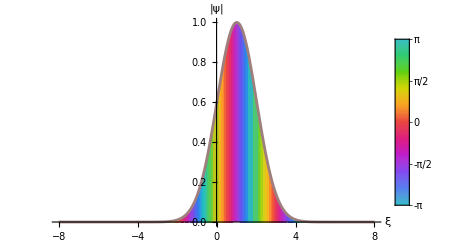

Save frames:

frames =Table[AbsArgPlot[waveFuncCoh[[1]]/.α->2 ⅇ^(-2ⅈ t),{ξ,-8,8},Filling->Axis,PlotLegends->Automatic,AxesLabel->{"ξ","|ψ|"}],{t,0,3,0.05}];

Save GIF locally:

Export[NotebookDirectory[]<>"Coh.GIF",frames,"GIF"];

If we have the not normalized superposition of coherent states 0.2 |α = 2 ⟩ + 0.5 |β ⟩. What is a possible value of β such there is probability zero of measuring two photons?

Solution

Get the relevant amplitude:

amplitude =(0.2 coherent[2]+0.5 coherent[x+ⅈ y])["Normalize"]["Amplitudes"][[3]];

Minimize the magnitude of the amplitude:

result =NMinimize[{Abs[amplitude],-1<=x<=1 &&-1<=y<=1},{x,y}]

{9.40196×10^-12,{x→1.10002×10^-12,y→-0.494693}}

Verify the answer with a probability plot:

(0.2 coherent[2]+0.5 coherent[x+ⅈ y /. result[[2]]])["Normalize"]["ProbabilityPlot"]

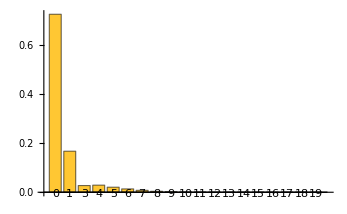

Consider the Kerr non-linear Hamiltonian χ (a^†a)^2. Describe the evolution a coherent state only under this Hamiltonian. Plot the fidelity of the evolved state respect to the initial coherent state. Do you see a periodic behavior? We consider ℏ = 1, use an appropriate value of χ and well a represented coherent state in the chosen truncation size

Solution

Kerr non-linearity:

HKerrNonLinear =QuantumOperator[χ(a^†@a)^2,"Parameters"->χ];

Initial coherent state:

ψ0 = coherent[0.6];

Evolved state:

evolved =QuantumEvolve[HKerrNonLinear[4.0],ψ0,{t,0,5}];

Plot the fidelity:

Plot[QuantumSimilarity[ψ0,evolved[t]],{t,0,5},AspectRatio->1/4,ImageSize->500]

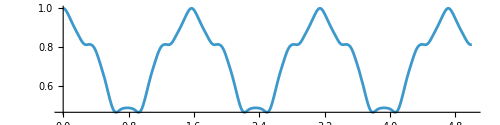

Changing α and χ varies the form of the curve and the period of the fidelity oscillations

References

Gerry, Christopher C. and Peter. L. Knight. 2005. Introductory Quantum Optics. Cambridge University Press.

Fox, Mark. 2006. Quantum Optics: An Introduction. Oxford: Oxford University Press.

Glauber, Roy J. 1963. Coherent and Incoherent States of the Radiation Field. Physical Review 131 (6): 2766–88.

Sudarshan, E. C. G. 1963. Equivalence of Semiclassical and Quantum Mechanical Descriptions of Statistical Light Beams. Physical Review Letters 10 (7): 277–79.

Klauder, John R., and Bo-Sture Skagerstam, eds. 1985. Coherent States: Applications in Physics and Mathematical Physics. Singapore: World Scientific.

Martin-Dussaud, Pierre. 2021. Searching for Coherent States: From Origins to Quantum Gravity. Quantum 5: 390.